# CFD Schemes For Testing

```mathematica
Clear["`*"]
```

## Kim Pentadiagonal 6th Order

```mathematica
kimPent6th[n_]:=Module[{P,Q,α,β,a0,a1,a2,a3,γ01,γ02,γ10,γ12,γ13,γ20,γ21,γ23,γ24,γS12,γS13,γS20,γS21,γS23,γS24,b22Filter,b00,b01,b02,b03,b04,b05,b06,b10,b11,b12,b13,b14,b15,b16,b20,b21,b22,b23,b24,b25,b26,bS11,bS12,bS13,bS14,bS15,bS16,bS21,bS22,bS23,bS24,bS25,bS26},
α=0.5862704032801503;
β=0.09549533555017055;
a1=0.6431406736919156;
a2=0.2586011023495066;
a3=0.007140953479797375;

γ01=5.912678614078549;
γ02=3.775623951744012;
γ10=0.08360703307833438;
γ12=2.058102869495757;
γ13=0.9704052014790193;
γ20=0.03250008295108466;
γ21=0.3998040493524358;
γ23=0.7719261277615860;
γ24=0.1626635931256900;

b01=-3.456878182643609;
b02=5.839043358834730;
b03=1.015886726041007;
b04=-0.2246526470654333;
b05=0.08564940889936562;
b06=-0.01836710059356763;
b00=-(b01+b02+b03+b04+b05+b06);
Print[b00];

b10=-0.3177447290722621;
b12=-0.02807631929593225;
b13=1.593461635747659;
b14=0.2533027046976367;
b15=-0.03619652460174756;
b16=0.004080281419108407;
b11=-(b10+b12+b13+b14+b15+b16);

b20=-0.1219006056449124;
b21=-0.6301651351188667;
b23=0.6521195063966084;
b24=0.3938843551210350;
b25=0.01904944407973912;
b26=-0.001027260523947668;
b22=-(b20+b21+b23+b24+b25+b26);

γS12=(γ12-γ10 γ02)/(1-γ10 γ01);
γS13=γ13/(1-γ10 γ01);
γS21=(γ10 γ21-γ20)/(γ10-γ20 γ12);
γS23=(γ10 γ23-γ20 γ13)/(γ10-γ20 γ12);
γS24=(γ10 γ24)/(γ10-γ20 γ12);

bS11=(b11-γ10 b01)/(1-γ10 γ01);
bS12=(b12-γ10 b02)/(1-γ10 γ01);
bS13=(b13-γ10 b03)/(1-γ10 γ01);
bS14=(b14-γ10 b04)/(1-γ10 γ01);
bS15=(b15-γ10 b05)/(1-γ10 γ01);
bS16=(b16-γ10 b06)/(1-γ10 γ01);

bS21=(γ10 b21-γ20 b11)/(γ10-γ20 γ12);
bS22=(γ10 b22-γ20 b12)/(γ10-γ20 γ12);
bS23=(γ10 b23-γ20 b13)/(γ10-γ20 γ12);
bS24=(γ10 b24-γ20 b14)/(γ10-γ20 γ12);
bS25=(γ10 b25-γ20 b15)/(γ10-γ20 γ12);
bS26=(γ10 b26-γ20 b16)/(γ10-γ20 γ12);

P=Table[0,{i,n},{j,n}];
P[[1,1]]=1;
P[[1,2]]=γS12;
P[[1,3]]=γS13;

P[[2,1]]=γS21;
P[[2,2]]=1;
P[[2,3]]=γS23;
P[[2,4]]=γS24;

P[[n,n]]=1;
P[[n,n-1]]=γ01;
P[[n,n-2]]=γ02;

P[[n-1,n]]=γ10;
P[[n-1,n-1]]=1;
P[[n-1,n-2]]=γ12;
P[[n-1,n-3]]=γ13;

P[[n-2,n]]=γ20;
P[[n-2,n-1]]=γ21;
P[[n-2,n-2]]=1;
P[[n-2,n-3]]=γ23;
P[[n-2,n-4]]=γ24;

Do[
P[[i,i]]=1;
If[(j==i-2)||(j==i+2), 
P[[i,j]]=β,
If[(j==i-1)||(j==i+1),
P[[i,j]]=α
]
]
,{i,3,n-3},{j,1,n}];

Q=Table[0,{i,n},{j,n}];
Q[[1,1]]=bS11;
Q[[1,2]]=bS12;
Q[[1,3]]=bS13;
Q[[1,4]]=bS14;
Q[[1,5]]=bS15;
Q[[1,6]]=bS16;

Q[[2,1]]=bS21;
Q[[2,2]]=bS22;
Q[[2,3]]=bS23;
Q[[2,4]]=bS24;
Q[[2,5]]=bS25;
Q[[2,6]]=bS26;

Q[[n,n]]=-b00;
Q[[n,n-1]]=-b01;
Q[[n,n-2]]=-b02;
Q[[n,n-3]]=-b03;
Q[[n,n-4]]=-b04;
Q[[n,n-5]]=-b05;
Q[[n,n-6]]=-b06;

Q[[n-1,n]]=-b10;
Q[[n-1,n-1]]=-b11;
Q[[n-1,n-2]]=-b12;
Q[[n-1,n-3]]=-b13;
Q[[n-1,n-4]]=-b14;
Q[[n-1,n-5]]=-b15;
Q[[n-1,n-6]]=-b16;

Q[[n-2,n]]=-b20;
Q[[n-2,n-1]]=-b21;
Q[[n-2,n-2]]=-b22;
Q[[n-2,n-3]]=-b23;
Q[[n-2,n-4]]=-b24;
Q[[n-2,n-5]]=-b25;
Q[[n-2,n-6]]=-b26;

Do[
If[(j==i-3), 
Q[[i,j]]=-a3,
If[(j==i+3),
Q[[i,j]]=a3,
If[(j==i-2), 
Q[[i,j]]=-a2,
If[(j==i+2),
Q[[i,j]]=a2,
If[(j==i-1), 
Q[[i,j]]=-a1,
If[(j==i+1),
Q[[i,j]]=a1
]
]
]
]
]
]
,{i,3,n-3},{j,1,n}];
Return[{Q,P}]
]
kimPent6th[20][[1]]//MatrixForm
kimPent6th[20][[2]]//MatrixForm
```

-3.24068

(-2.33321 | -1.02097 | 2.98329 | 0.538081 | -0.0857445 | 0.0111061 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.296033 | -1.50549 | 0.16354 | 1.47735 | 0.165628 | -0.0130691 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
-0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00714095 | -0.258601 | -0.643141 | 0 | 0.643141 | 0.258601 | 0.00714095
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.00102726 | -0.0190494 | -0.393884 | -0.65212 | 0.31196 | 0.630165 | 0.121901
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -0.00408028 | 0.0361965 | -0.253303 | -1.59346 | 0.0280763 | 1.46883 | 0.317745
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0183671 | -0.0856494 | 0.224653 | -1.01589 | -5.83904 | 3.45688 | 3.24068)

-3.24068

(1 | 3.44587 | 1.91909 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0554085 | 1 | 1.97387 | 0.813458 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.0954953 | 0.58627 | 1 | 0.58627 | 0.0954953 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.162664 | 0.771926 | 1 | 0.399804 | 0.0325001
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0.970405 | 2.0581 | 1 | 0.083607
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 3.77562 | 5.91268 | 1)

```mathematica
kimPent6thFilters[n_,κc_]:=Module[{R,S, α, β,γ, bS,γS,b,a,A,c,d},
A=30-5Cos[κc]+10Cos[2κc]-3Cos[3κc];
α=-(30Cos[κc]+2Cos[3κc])/A;
Print["α: "<>ToString[α]];
β=(18+9Cos[κc]+6Cos[2κc]-Cos[3κc])/(2A);
Print["β: "<>ToString[β]];

a={0,30/A Cos[κc/2]^4,0,0};
a[[3]]=-(2a[[2]])/5;
a[[4]]=a[[2]]/15;
a[[1]]=-2(a[[2]]+a[[3]]+a[[4]]);
Print["a_(0 - 3): "<>ToString[a]];

c=1+β(5+4β+60 β^2)+5(1+3β+10 β^2)α+2(4+11β)α^2+5 α^3;
d=(1-β)(1+6β+60 β^2)+(5+35β-29 β^2)α+(9-5β)α^2;

γ={{1,1/c(α(1+α)(1+4α)+2α(7+3α)β+24(1-α)β^2-80 β^3),1/c(α^3+(1+3α+14 α^2)β+46α β^2+60 β^3)},{1/d(10 β^2(8β-1)+(1+4β+81 β^2)α+5(1+8β)α^2+9 α^3),1,1/d(α(1+5α+9 α^2)+α(5+36α)β+(55α-1)β^2+10 β^3),β/d(1+5α+9 α^2+5(1+7α)β+50 β^2)},{β,α,1,α,β}};
Print["γ_(00 - 02): "<>ToString[γ[[1]]]];
Print["γ_(10 - 13): "<>ToString[γ[[2]]]];
Print["γ_(20 - 24): "<>ToString[γ[[3]]]];

b={a[[3]]+5a[[4]],a[[2]]-10a[[4]],0,a[[2]]-5a[[4]],a[[3]]+a[[4]],a[[4]]};
b[[3]]=-(Sum[b[[i]],{i,1,6}]);
Print["b_(20 - 25): "<>ToString[b]];

γS={{1,(γ[[2,3]]-γ[[2,1]]*γ[[1,3]])/(1-γ[[2,1]]*γ[[1,2]]),γ[[2,4]]/(1-γ[[2,1]]*γ[[1,2]])},{(γ[[2,1]]*γ[[3,2]]-γ[[3,1]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),1,(γ[[2,1]]*γ[[3,4]]-γ[[3,1]]*γ[[2,4]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]),(γ[[2,1]]*γ[[3,5]])/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]])}};
Print["(γ^*)_(11 - 13): "<>ToString[γ[[1]]]];
Print["(γ^*)_(21 - 24): "<>ToString[γ[[2]]]];

bS=Table[γ[[2,1]]*b[[i]],{i,2,6}]/(γ[[2,1]]-γ[[3,1]]*γ[[2,3]]);
Print["(b^*)_(21 - 25): "<>ToString[bS]];

R=IdentityMatrix[n];
R[[1,2]]=γS[[1,2]];R[[1,3]]=γS[[1,3]];
R[[2,1]]=γS[[2,1]]; R[[2,3]]=γS[[2,3]]; R[[2,4]]=γS[[2,4]];
R[[n,n-1]]=γ[[1,2]];R[[n,n-2]]=γS[[1,3]];
R[[n-1,n]]=γ[[2,1]]; R[[n-1,n-2]]=γ[[2,3]]; R[[n-1,n-3]]=γ[[2,4]];
R[[n-2,n]]=γ[[3,1]]; R[[n-2,n-1]]=γ[[3,2]]; R[[n-2,n-3]]=γ[[3,4]]; R[[n-2,n-4]]=γ[[3,5]];
Do[
If[(j==i-2)||(j==i+2), 
R[[i,j]]=β,
If[(j==i-1)||(j==i+1),
R[[i,j]]=α
]
],{i,3,n-3},{j,1,n}];

S=Table[0,{i,n},{j,n}];
Do[S[[2,i]]=bS[[i]]; S[[n-2,n-i+1]]=b[[i]],{i,1,5}];
S[[n-2,n-5]]=b[[6]];
Do[
If[j>=i-3&&j<=i+3,
S[[i,j]]=a[[Abs[i-j]+1]]
]
,{i,3,n-3},{j,1,n}];

Return[{R,S}]
]
```

```mathematica
{Q,P}=kimPent6th[50];
Q//MatrixForm;
P//MatrixForm;
```

-3.24068

```mathematica
{R,S}=kimPent6thFilters[50,0.85π];
R//MatrixForm;
S//MatrixForm;
```

α: 0.662785

β: 0.167443

a_(0 - 3): {-0.00291151, 0.00218363, -0.000873452, 0.000145575}

γ_(00 - 02): {1, 0.398599, 0.20084}

γ_(10 - 13): {0.786059, 1, 0.730279, 0.180977}

γ_(20 - 24): {0.167443, 0.662785, 1, 0.662785, 0.167443}

b_(20 - 25): {-0.000145575, 0.000727876, -0.00145575, 0.00145575, -0.000727876, 0.000145575}

(γ^*)_(11 - 13): {1, 0.398599, 0.20084}

(γ^*)_(21 - 24): {0.786059, 1, 0.730279, 0.180977}

(b^*)_(21 - 25): {0.000861964, -0.00172393, 0.00172393, -0.000861964, 0.000172393}

```mathematica
Q.(IdentityMatrix[50]+Inverse[R].S)//MatrixForm;
```

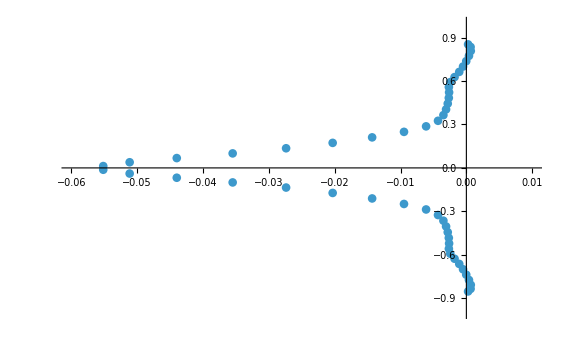

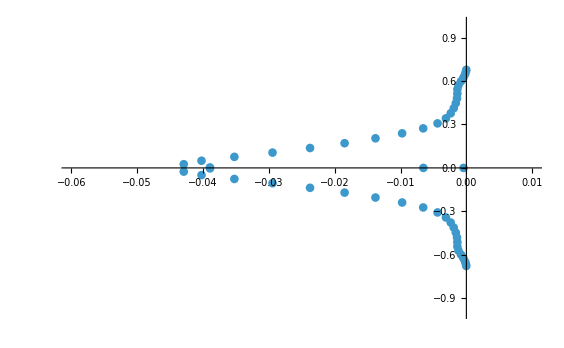

```mathematica
QNew=Q;
QNew[[1]]=Table[0,{i,Length[Q]}];

PNew=P;
PNew[[1]]=Table[0,{i,1,Length[P]}];
PNew[[1,1]]=1;

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,1]],1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,1]],1]];

noFilter=Eigenvalues[-Inverse[P].Q]/π;
filterAttempt=Eigenvalues[-Inverse[P].(Q.(IdentityMatrix[50]+Inverse[R].S))]/π;
(*noFilterDrop=Eigenvalues[-PDrop.QDrop];
noFilterNew=Eigenvalues[-Inverse[PNew].QNew];*)

ComplexListPlot[noFilter,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.01},{-1,1}}]
ComplexListPlot[filterAttempt,AspectRatio->1/GoldenRatio,PlotRange->{{-0.06,0.01},{-1,1}}]

(*ComplexListPlot[noFilterDrop,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,1]],1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,-1]],-1]];
Eigenvalues[PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,-1]],-1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,-1]],-1]];
Eigenvalues[PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

PDrop=Inverse[Transpose[Drop[Transpose[Drop[P,-1]],-1]]];
QDrop=Transpose[Drop[Transpose[Drop[Q,1]],1]];
Eigenvalues[-PDrop.QDrop];
ComplexListPlot[%,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]

ComplexListPlot[noFilterNew,AspectRatio->1/GoldenRatio,PlotRange->{All,All}]*)
(*Max[Re[noFilter]]*)
```